```mathematica
Sum[ x^(-s k)/k!,{k,0,Infinity}]
```

ⅇ^(x^-s)

```mathematica
N@(x^s/(-1+x^s))/.x->3/.s->3
```

1.03846

```mathematica
N@1/(1-x^-s)/.x->3/.s->3
```

1.03846

```mathematica
Product[ (1/(1-x^-s))^(MoebiusMu[k]/k),{k,1,Infinity}]
```

1

```mathematica
N@Table[ E^(2^-2/k),{k,1,10}]
```

{1.28403,1.13315,1.0869,1.06449,1.05127,1.04255,1.03636,1.03174,1.02817,1.02532}

```mathematica
N[1/(1-2^-2)]
```

1.33333

```mathematica
Clear[l2mx]
l2mx[n_,k_]:=l2mx[n,k]=Sum[ -(2^j-1)/j l2mx[n-j,k-1],{j,1,n-1}]
l2mx[n_,1]:=-(2^n-1)/n
l2mx[n_,0]:=If[n==0,1,0]
f2mx[n_,z_]:=Sum[ z^k/k! l2mx[n,k],{k,0,n}]
```

```mathematica
Table[f2mx[n,1],{n,0,10}]
```

{1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
Series[2^(1)-1/(1-x^-2),{x,0,20}]
```

2+x^2+x^4+x^6+x^8+x^10+x^12+x^14+x^16+x^18+x^20+O[x]^21

```mathematica
Series[(2x^2-1)/(x^2-1),{x,0,20}]
```

1-x^2-x^4-x^6-x^8-x^10-x^12-x^14-x^16-x^18-x^20+O[x]^21

```mathematica
Series[(1-2x^2)/(1-x^2),{x,0,20}]
```

1-x^2-x^4-x^6-x^8-x^10-x^12-x^14-x^16-x^18-x^20+O[x]^21

```mathematica
Series[(1-2x^-s)/(1-x^-s),{x,0,20}]
```

(1-2 x^-s)/(1-x^-s)

```mathematica
D[(1-2x^-s)^z,z]/.z->0
```

Log[1-2 x^-s]

```mathematica
Series[ 1/(1-2x^1),{x,0,20}]
```

1+2 x+4 x^2+8 x^3+16 x^4+32 x^5+64 x^6+128 x^7+256 x^8+512 x^9+1024 x^10+2048 x^11+4096 x^12+8192 x^13+16384 x^14+32768 x^15+65536 x^16+131072 x^17+262144 x^18+524288 x^19+1048576 x^20+O[x]^21

```mathematica
Sum[ 1/k! x^(-s k),{k,0,Infinity}]
```

ⅇ^(x^-s)

```mathematica
Sum[ 1/k! 2^k x^(-s k),{k,0,Infinity}]
```

ⅇ^(2 x^-s)

```mathematica
FullSimplify[ⅇ^(x^-s)/ⅇ^(2 x^-s)]
```

ⅇ^(-x^-s)

```mathematica
Sum[ (-1)^k/k! x^(-s k),{k,0,Infinity}]
```

ⅇ^(-x^-s)

```mathematica
N[E^-(2^-3)Product[ E^(Prime[j]^-3),{j,2,160}]]
```

0.927523

```mathematica
N@Product[ (((1-2^(1-3))Zeta[3 k]))^(MoebiusMu[k]/k),{k,1,300}]
```

1.19457

```mathematica
FullSimplify[((1-2^(1-s))/(1-2^-s))Product[ 1/(1-Prime[j]^-s),{j,2,Infinity}]]
```

2^-s (-2+2^s) Zeta[s]

```mathematica
Expand[2^-s (-2+2^s)]
```

1-2^(1-s)

```mathematica
Series[1/(1-2x),{x,0,10}]
```

1+2 x+4 x^2+8 x^3+16 x^4+32 x^5+64 x^6+128 x^7+256 x^8+512 x^9+1024 x^10+O[x]^11

```mathematica
Table[Integrate[ x^k,x]/.x->1,{k,0,10}]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11}

```mathematica
Table[Integrate[ 2^k x^k,x]/.x->1,{k,0,10}]
```

{1,1,4/3,2,16/5,16/3,64/7,16,256/9,256/5,1024/11}

```mathematica
Table[2^k/(k+1),{k,0,10}]
```

{1,1,4/3,2,16/5,16/3,64/7,16,256/9,256/5,1024/11}

```mathematica
A1[n_]:=HarmonicNumber[Floor[n]]
A2[n_]:=Sum[ 2^(k-1)/(k),{k,1,n}]
mA1[n_]:=Sum[ MoebiusMu[k]/k A1[n/k],{k,1,n}]
mA2[n_]:=Sum[ MoebiusMu[k]/k A2[n/k],{k,1,n}]
```

```mathematica
Table[mA2[n],{n,1,10}]
```

{1,3/2,5/2,4,7,23/2,41/2,71/2,127/2,113}

```mathematica
Table[mA1[n],{n,1,10}]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
Table[A1[n],{n,1,10}]
```

{1,3/2,11/6,25/12,137/60,49/20,363/140,761/280,7129/2520,7381/2520}

```mathematica
Table[A2[n],{n,1,10}]
```

{1,2,10/3,16/3,128/15,208/15,2416/105,4096/105,21248/315,37376/315}

```mathematica
pf[n_]:=Sum[ Sum[ MoebiusMu[d] 2^(m/d-1)/m,{d,Divisors[m]}],{m,1,n}]
```

```mathematica
Table[pf[n],{n,1,10}]
```

{1,3/2,5/2,4,7,23/2,41/2,71/2,127/2,113}

```mathematica
A2[2]-1/2A2[1]
```

3/2

```mathematica
A2[3]
```

10/3

```mathematica
Sum[Pochhammer[z,k]/k! x^k,{k,0,Infinity}]
```

(1-x)^-z

```mathematica
Sum[Pochhammer[z,k]/k!2^k  x^k,{k,0,Infinity}]
```

(1-2 x)^-z

```mathematica
Sum[Pochhammer[z,k]/k!(-1)^k  x^k,{k,0,Infinity}]
```

(1+x)^-z

```mathematica
Sum[  x^(2k),{k,0,Infinity}]
```

1/(1-x^2)

```mathematica
Sum[Pochhammer[z,k]/k! x^(2k),{k,0,Infinity}]
```

(1-x^2)^-z

```mathematica
CoefficientList[Series[Log[1-x],{x,0,20}],x]
```

{0,-1,-1/2,-1/3,-1/4,-1/5,-1/6,-1/7,-1/8,-1/9,-1/10,-1/11,-1/12,-1/13,-1/14,-1/15,-1/16,-1/17,-1/18,-1/19,-1/20}

```mathematica
iv[n_]:=Sum[ (-1)^(k+1)/k,{k,1,n}]
```

```mathematica
iv[1]
```

1

```mathematica
iv[2]-(1/2)iv[1]
```

0

```mathematica
InverseSeries[Series[Log[1/(1-x)],{x,0,10}]]
```

x-x^2/2+x^3/6-x^4/24+x^5/120-x^6/720+x^7/5040-x^8/40320+x^9/362880-x^10/3628800+O[x]^11

```mathematica
Clear[pp]
pp[n_,k_]:=pp[n,k]=Sum[ (-1)^(j+1)/j pp[Floor[n/j],k-1],{j,2,n}]
pp[n_,0]:=UnitStep[n-1]
ppz[n_,z_]:=Sum[bin[z,k]pp[n,k],{k,0,Log2@n}]
```

```mathematica
Table[ppz[n,-1]-ppz[n-1,-1],{n,1,10}]
```

{1,1/2,-1/3,1/2,-1/5,-1/6,-1/7,1/2,0,-1/10}

```mathematica
N@ppz[1000000,-1]
```

1.18562

```mathematica
2^(z 1.1856200038814326)/.z->1
```

2.27461

```mathematica
Sum[ (ppz[j,-1]-ppz[j-1,-1])ppz[100/j,1],{j,1,100}]
```

1

```mathematica
Log[2.]
```

0.693147

```mathematica
A1[n_]:=Sum[ 1/(k) x^k,{k,1,n}]
A2[n_]:=Sum[ 2^(k-1)/(k) x^k,{k,1,n}]
A2a[n_]:=2^(n-1)A1[n]-Sum[ 2^(k-1) A1[k],{k,1,n-1}]
```

```mathematica
A1[5]
```

x+x^2/2+x^3/3+x^4/4+x^5/5

```mathematica
Expand[16A1[5]-8A1[4]-4A1[3]-2A1[2]-A1[1]]
```

x+x^2+(4 x^3)/3+2 x^4+(16 x^5)/5

```mathematica
A2[5]
```

x+x^2+(4 x^3)/3+2 x^4+(16 x^5)/5

```mathematica
Expand[32A1[6]-16A1[5]-8A1[4]-4A1[3]-2A1[2]-A1[1]]
```

x+x^2+(4 x^3)/3+2 x^4+(16 x^5)/5+(16 x^6)/3

```mathematica
A2[6]
```

x+x^2+(4 x^3)/3+2 x^4+(16 x^5)/5+(16 x^6)/3

```mathematica
Expand[A2a[6]]
```

x+x^2+(4 x^3)/3+2 x^4+(16 x^5)/5+(16 x^6)/3

```mathematica
Expand[E^(2^-s) E^(-2^(1-s))]
```

ⅇ^(-2^(1-s)+2^-s)

```mathematica
N[E^(-2^(-s))Product[E^(Prime[j]^-s),{j,2,Infinity}]/.s->3]
```

0.927523

```mathematica
N[E^(-2^(1-s))Product[E^(Prime[j]^-s),{j,1,Infinity}]/.s->3]
```

0.927523

```mathematica
N@Product[ (((1-2^(k(1-3)))Zeta[3 k]))^(MoebiusMu[k]/k),{k,1,300}]
```

0.927523

```mathematica
N[Product[E^(Prime[j]^-s),{j,1,Infinity}]/.s->3]
```

1.19096

```mathematica
N@Product[ Zeta[3 k]^(MoebiusMu[k]/k),{k,1,300}]
```

1.19096

```mathematica
N[Product[ (1/(1-x^(k(-s))))^(MoebiusMu[k]/k),{k,1,100}]/.x->2/.s->3]
```

1.13315

```mathematica
N[E^(2^-3)]
```

1.13315

```mathematica
N[Product[ (1/(1-x^(k(1-s))))^(-MoebiusMu[k]/k),{k,1,100}]/.x->2/.s->3]
```

0.778801

```mathematica
N[E^(-(2^(1-3)))]
```

0.778801

```mathematica
FullSimplify[E^(-(2^(1-s))) E^(2^(-s))]
```

ⅇ^(-2^-s)

```mathematica
Sum[ 3^(-b s)/b!,{b,0,Infinity}]
```

ⅇ^(3^-s)

```mathematica
Sum[(-1)^b  2^(-b s)/b!,{b,0,Infinity}]
```

ⅇ^(-2^-s)

```mathematica
Clear[pd,ps]
ps[n_,s_]:=ps[n,s]=N@Sum[Prime[j]^-s,{j,1,PrimePi[n]}]
pr[n1_,n2_,s_]:=ps[n2,s]-ps[n1,s]+1
pd[n_,s_, k_]:=pd[n,s,k]=If[n<Prime[k],1,Sum[N[ Prime[k]^(-a s)/a!] pd[Floor[n/Prime[k]^a],s,k+1],{a,0,Log[Prime[k],n]}]]
pda[n_,s_, k_]:=pda[n,s,k]=If[n<Prime[k],1,If[n < Prime[k]^2, pr[Prime[k],n,s], Sum[N[ Prime[k]^(-a s)/a!] pda[Floor[n/Prime[k]^a],s,k+1],{a,0,Log[Prime[k],n]}]]]
pdb[n_,s_, k_]:=If[n<Prime[k],1,If[n < Prime[k]^2, pr[Prime[k],n,s], Sum[N[ (-1)^a Prime[k]^(-a s)/a!] pda[Floor[n/Prime[k]^a],s,k+1],{a,0,Log[Prime[k],n]}]]]
pdc[n_,s_, k_]:=pdc[n,s,k]=If[n<Prime[k],1,Sum[N[ (-1)^a Prime[k]^(-a s)/a!] pd[Floor[n/Prime[k]^a],s,k+1],{a,0,Log[Prime[k],n]}]]
```

```mathematica
pd[100000,2,1]
```

1.57183

```mathematica
$RecursionLimit = 1000000
```

1000000

```mathematica
Zeta[2.]
```

1.64493

```mathematica
Prime[5]
```

11

```mathematica
pd[100,2,5]
```

124020778002215450777436066242054922242650889014310897895124981018510/120536136879181028275917507552308234524376627510960757059061829251289

```mathematica
PrimePi[100]-PrimePi[10] + 1
```

22

```mathematica
ps[100,2]-ps[10,2]+1
```

124020778002215450777436066242054922242650889014310897895124981018510/120536136879181028275917507552308234524376627510960757059061829251289

```mathematica
pdb[1000000,N[ZetaZero[1]],1]
```

9.7203+16.1394 ⅈ

```mathematica
pdc[10000,N[ZetaZero[1]],1]
```

$Aborted

```mathematica
Clear[dz]
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_]:=dz[n]=Product[1/(p[[2]]!),{p,FI[n]}]
sdz[n_,s_]:= Sum[ dz[j] j^-s,{j,1,n,2}]
si[n_,s_]:=Sum[N[ (-1)^a 2^(-a s)/a!] sdz[Floor[n/2^a],s],{a,0,Log[2,n]}]
```

```mathematica
pdc[100000,.5,1]
```

169.623

```mathematica
si[100000, 3]
```

0.927523

```mathematica
N@Product[ (((1-2^(k(1-2)))Zeta[2 k]))^(MoebiusMu[k]/k),{k,1,300}]
```

0.95337

```mathematica
(((1-2^((1-.5)))Zeta[.5]))
```

0.604899

```mathematica
N[E^(-2^(1-s))Product[E^(-Prime[j]^-s),{j,1,Infinity}]/.s->.5]
```

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Indeterminate

```mathematica
Clear[oz]
oz[0,z_]:=1
oz[n_,z_]:=oz[n,z]=Product[z^p[[2]]/(p[[2]]!),{p,FI[n]}]
dzo[n_,z_]:=Product[Pochhammer[z,p[[2]]]/(p[[2]]!),{p,FI[n]}]
moz[n_,s_,k_]:=Sum[ dzo[j,MoebiusMu[k]/k]j^(-s k) moz[Floor[n/j^k],s,k-1],{j,1,If[k==1,n,Floor[Log[k,n]]]}]
moz[n_,s_,0]:=1
mzz[n_,s_]:=moz[n,s,Floor[Log[2,n]]+1]
```

```mathematica
Table[mzz[n,1]-mzz[n-1,1],{n,2,10}]
```

{1/2,1/3,1/8,1/5,1/6,1/7,1/16,1/18,1/10}

```mathematica
oz[1,z]
```

1

```mathematica
Log[2.,10]
```

3.32193

```mathematica
Clear[pe]
pe[n_,s_,k_]:=pe[n,s,k]=N@Sum[ (-1)^(j+1)j^-s pe[n-j,s,k-1],{j,1,n-1}]
pe[n_,s_,1]:=(-1)^(n+1)n^-s
pe[n_,s_,0]:=If[n==0,1,0]
pa[n_,s_,z_]:=Sum[ z^k/k! pe[n,s,k],{k,0,n}]
pas[n_,s_,z_]:=Sum[ pa[j,s,z],{j,0,n}]
peo[n_,s_,k_]:=peo[n,s,k]=N@Sum[ j^-s peo[n-j,s,k-1],{j,1,n-1}]
peo[n_,s_,1]:=n^-s
peo[n_,s_,0]:=If[n==0,1,0]
pao[n_,s_,z_]:=Sum[ z^k/k! peo[n,s,k],{k,0,n}]
Chop@Table[pa[n,2,-1],{n,0,30}]
```

{1,-1,0.75,-0.527778,0.371528,-0.267083,0.197157,-0.14943,0.116041,-0.0920854,0.0744801,-0.0612542,0.0511188,-0.0432119,0.0369442,-0.0319041,0.0277988,-0.0244159,0.0215989,-0.0192309,0.0172231,-0.0155073,0.0140304,-0.0127507,0.0116352,-0.0106574,0.00979569,-0.00903277,0.00835423,-0.00774824,0.00720492}

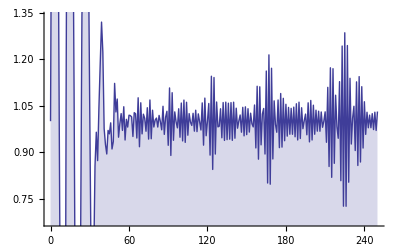

```mathematica
DiscretePlot[{Re[pas[n,.5+21.022I,1]]},{n,0,250}]
```

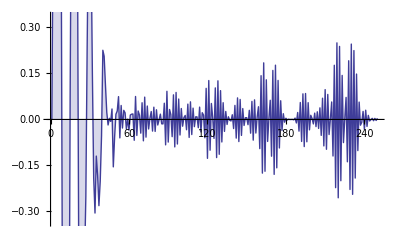

```mathematica
DiscretePlot[{Im[pas[n,.5+21.022I,1]]},{n,0,250}]
```

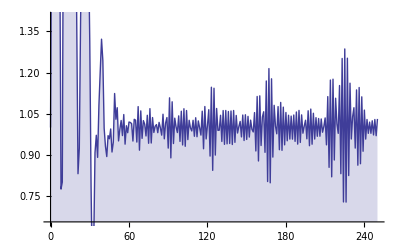

```mathematica
DiscretePlot[{Abs[pas[n,.5+21.022I,1]]},{n,0,250}]
```

```mathematica
N[E^(Pi^2/12)]
```

2.27611

```mathematica
N@ZetaZero[2]
```

0.5+21.022 ⅈ

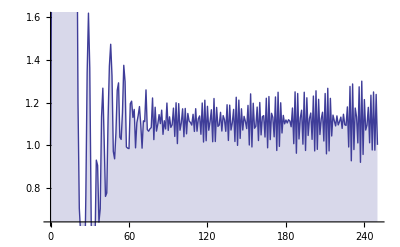

```mathematica
DiscretePlot[{Re[pas[n,.5+31I,1]]},{n,0,250}]
```

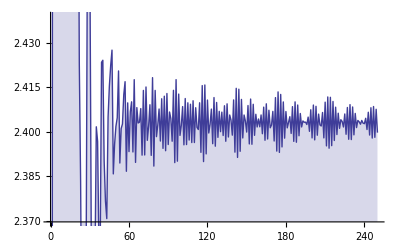

```mathematica
DiscretePlot[{Re[pas[n,.8+31I,1]]},{n,0,250}]
```

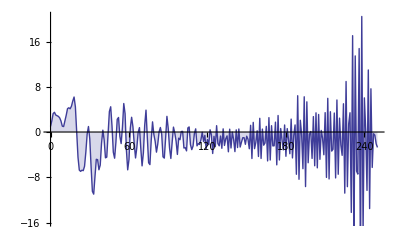

```mathematica
DiscretePlot[{Re[pas[n,.2+31I,1]]},{n,0,250}]
```

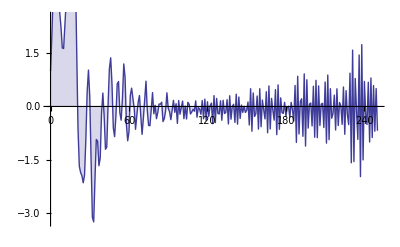

```mathematica
DiscretePlot[{Re[pas[n,.35+31I,1]]},{n,0,250}]
```

```mathematica
DiscretePlot[{Re[pas[n,.2+31I,1]]},{n,0,250}]
```

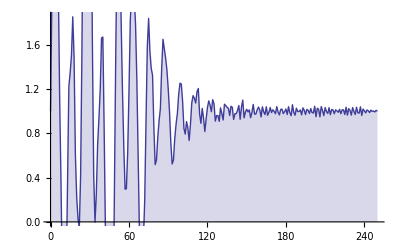

```mathematica
DiscretePlot[{Re[pas[n,N[ZetaZero[12]],1]]},{n,0,250}]
```

```mathematica
N[ZetaZero[12]]
```

0.5+56.4462 ⅈ

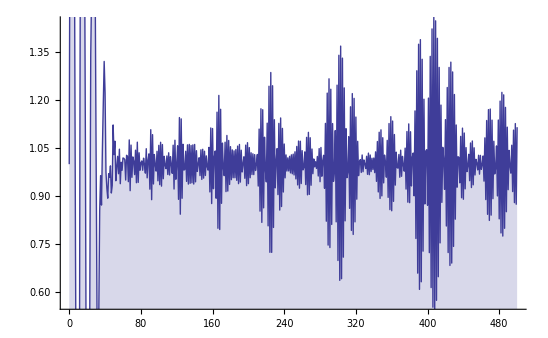

```mathematica
DiscretePlot[{Re[pas[n,.5+21.022I,1]]},{n,0,500}]
```

```mathematica
det[n_,s_]:=Sum[ (-1)^(j+1) j^-s,{j,1,n}]
```

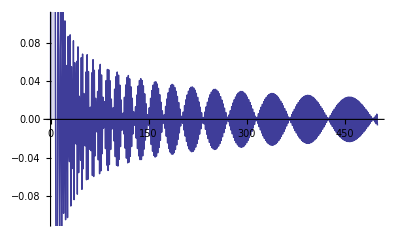

```mathematica
DiscretePlot[Re[det[n,.5+21.022I]],{n,0,500}]
```

```mathematica
det[10,.5+I]
```

0.74872+0.302933 ⅈ

```mathematica
DiscretePlot[{Re[pas[n,.5+21.022I,1]]},{n,0,250}]
```

-Graphics-

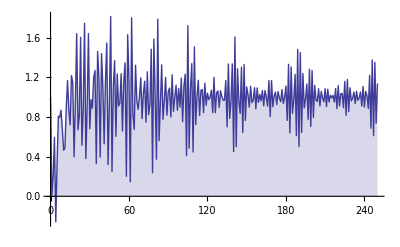

```mathematica
DiscretePlot[{Re[pas[n,.5+21.022I,-1]]},{n,0,250}]
```

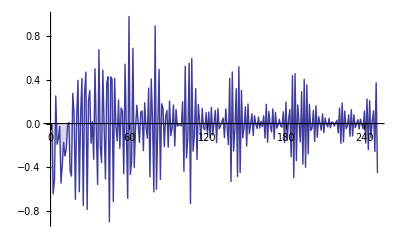

```mathematica
DiscretePlot[{Im[pas[n,.5+21.022I,-1]]},{n,0,250}]
```

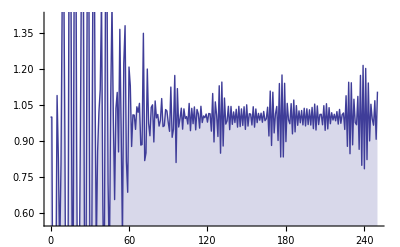

```mathematica
DiscretePlot[{Re[pas[n,.5+21.022I,I]]},{n,0,250}]
```

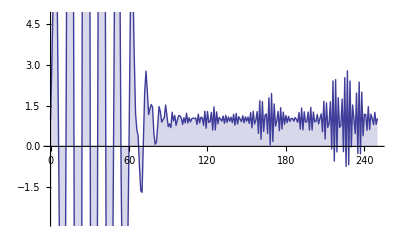

```mathematica
DiscretePlot[{Re[pas[n,.5+21.022I,2]]},{n,0,250}]
```

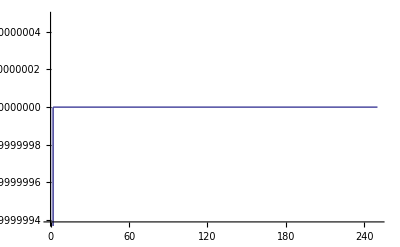

```mathematica
DiscretePlot[{Re[pas[n,1,2]]},{n,0,250}]
```

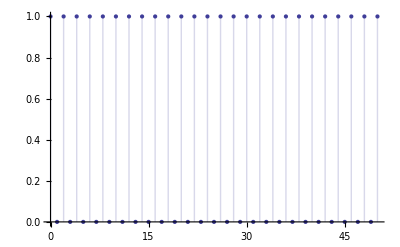

```mathematica
DiscretePlot[{Re[pas[n,1,-1]]},{n,0,50}]
```